# Practical - 2

## To solve 2nd order differential equation and plotting its solutions

## Question - 1: y’’ + y’ - 6y = 0

-6 y[x]+y'[x]+y''[x]==0

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

{{y[x]→(ⅇ^(-3 x) (-9 ⅇ^6+2 ⅇ^10+3 ⅇ^(5 x)+9 ⅇ^(6+5 x)))/(3+2 ⅇ^10)}}

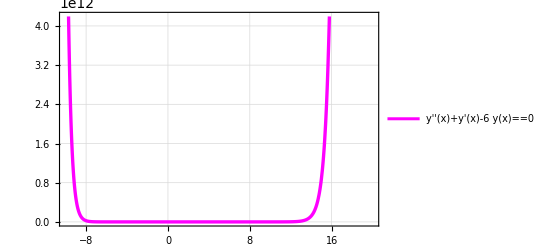

```mathematica
eq1=y''[x]+y'[x]-6*y[x]==0
DSolve[{y''[x]+y'[x]-6*y[x]==0},y[x],x]
sol1 = DSolve[{y''[x]+y'[x]-6*y[x]==0,y[0]==1,y'[2]==9},y[x],x]
Plot[y[x]/.sol1,{x,-10,20},PlotLegends->{eq1},PlotStyle->{{Magenta,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 2 : y’’ - 9y’ + 20y = sin x

20 y[x]+9 y'[x]+y''[x]==Sin[x]

{{y[x]→ⅇ^(-5 x) C[1]+ⅇ^(-4 x) C[2]+1/442 (-9 Cos[x]+19 Sin[x])}}

{{y[x]→-1/(442 (-5+4 ⅇ^2))ⅇ^(-5 x) (-3572 ⅇ^2-3094 ⅇ^10+4465 ⅇ^x+3094 ⅇ^(10+x)+19 ⅇ^10 Cos[2]-19 ⅇ^(10+x) Cos[2]-45 ⅇ^(5 x) Cos[x]+36 ⅇ^(2+5 x) Cos[x]+9 ⅇ^10 Sin[2]-9 ⅇ^(10+x) Sin[2]+95 ⅇ^(5 x) Sin[x]-76 ⅇ^(2+5 x) Sin[x])}}

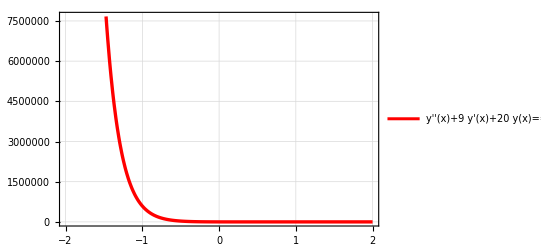

```mathematica
eq1=y''[x]+9*y'[x]+20*y[x]==Sin[x]
DSolve[{y''[x]+9*y'[x]+20*y[x]==Sin[x]},y[x],x]
sol2 = DSolve[{y''[x]+9*y'[x]+20*y[x]==Sin[x],y[0]==2,y'[2]==7},y[x],x]
Plot[y[x]/.sol2,{x,-2,2},PlotLegends->{eq1},PlotStyle->{{Red,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 3: y’’ - 6y’ + 5y = e-3x

5 y[x]-6 y'[x]+y''[x]==ⅇ^(-3 x)

{{y[x]→ⅇ^(-3 x)/32+ⅇ^x C[1]+ⅇ^(5 x) C[2]}}

{{y[x]→-(ⅇ^(-8-3 x) (ⅇ^8-5 ⅇ^16+3 ⅇ^(4 x)-3 ⅇ^(8 x)+224 ⅇ^(6+4 x)-635 ⅇ^(16+4 x)-224 ⅇ^(6+8 x)+127 ⅇ^(8+8 x)))/(32 (-1+5 ⅇ^8))}}

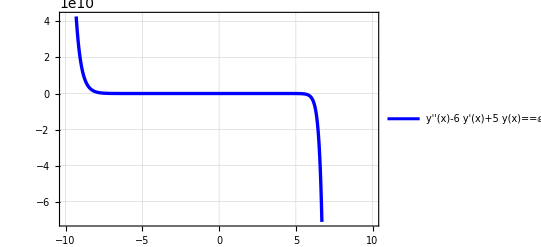

```mathematica
eq1= y''[x]-6*y'[x]+5*y[x]==ⅇ^(-3*x)
DSolve[{y''[x]-6*y'[x]+5*y[x]==ⅇ^(-3*x)},y[x],x]
sol2 = DSolve[{y''[x]-6*y'[x]+5*y[x]==ⅇ^(-3*x),y[0]==4,y'[2]==7},y[x],x]
Plot[y[x]/.sol2,{x,-2,2}]
Plot[y[x]/.sol2,{x,-10,10},PlotLegends->{eq1},PlotStyle->{{Blue,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 4: y''[x]-4*y'[x]+13*y[x]==(ⅇ^(2*x))*Cos[3*x]

13 y[x]-4 y'[x]+y''[x]==ⅇ^(2 x) Cos[3 x]

{{y[x]→ⅇ^(2 x) C[2] Cos[3 x]+ⅇ^(2 x) C[1] Sin[3 x]+1/36 ⅇ^(2 x) (Cos[3 x] Cos[6 x]+6 x Sin[3 x]+Sin[3 x] Sin[6 x])}}

{{y[x]→1/(36 (3 Cos[9]+2 Sin[9]))ⅇ^(-6+2 x) (321 ⅇ^6 Cos[9] Cos[3 x]+3 ⅇ^6 Cos[9] Cos[3 x] Cos[6 x]+214 ⅇ^6 Cos[3 x] Sin[9]+2 ⅇ^6 Cos[3 x] Cos[6 x] Sin[9]+144 Sin[3 x]-268 ⅇ^6 Cos[9] Sin[3 x]+18 ⅇ^6 x Cos[9] Sin[3 x]-2 ⅇ^6 Cos[9] Cos[18] Sin[3 x]+279 ⅇ^6 Sin[9] Sin[3 x]+12 ⅇ^6 x Sin[9] Sin[3 x]-3 ⅇ^6 Cos[18] Sin[9] Sin[3 x]+3 ⅇ^6 Cos[9] Sin[18] Sin[3 x]-2 ⅇ^6 Sin[9] Sin[18] Sin[3 x]+3 ⅇ^6 Cos[9] Sin[3 x] Sin[6 x]+2 ⅇ^6 Sin[9] Sin[3 x] Sin[6 x])}}

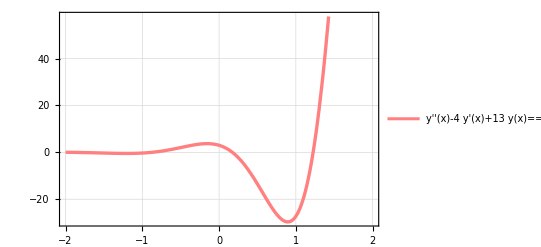

```mathematica
eq1= y''[x]-4*y'[x]+13*y[x]==(ⅇ^(2*x))*Cos[3*x]
DSolve[{y''[x]-4*y'[x]+13*y[x]==(ⅇ^(2*x))*Cos[3*x]},y[x],x]
sol4 = DSolve[{y''[x]-4*y'[x]+13*y[x]==(ⅇ^(2*x))*Cos[3*x],y[0]==3,y'[3]==4},y[x],x]
Plot[y[x]/.sol4,{x,-2,2},PlotLegends->{eq1},PlotStyle->{{Pink,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 5 :

{{y[x]→ⅇ^(-1. x) C[2] Cos[2. x]+ⅇ^(-1. x) C[1] Sin[2. x]+2. ⅇ^(-1. x) (0.+0.08 ⅇ^(1.5 x) Cos[2. x]^2+0.08 ⅇ^(1.5 x) Sin[2. x]^2+1. ⅇ^(1. x) Cos[2. x]^2 Sin[10. x]+1. ⅇ^(1. x) Sin[2. x]^2 Sin[10. x])}}

{{y[x]→2. ⅇ^(-1. x) (-14.4216 Cos[2. x]+0.08 ⅇ^(1.5 x) Cos[2. x]^2-20.6763 Sin[2. x]+0.08 ⅇ^(1.5 x) Sin[2. x]^2+1. ⅇ^(1. x) Cos[2. x]^2 Sin[10. x]+1. ⅇ^(1. x) Sin[2. x]^2 Sin[10. x])}}

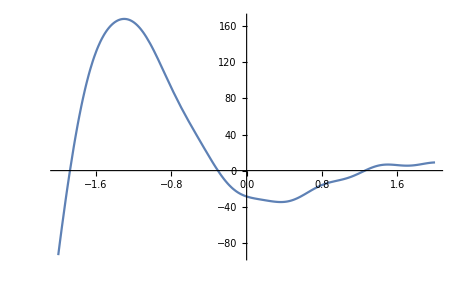

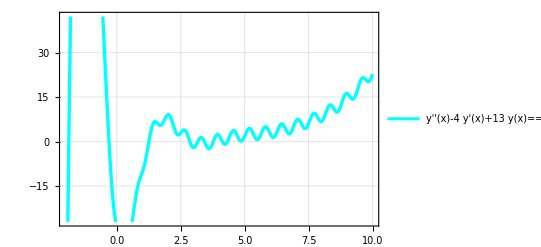

```mathematica
DSolve[{y''[x]+2*y'[x]+5*y[x]==ⅇ^(0.5*x)+40*Cos[10*x]-190*Sin[10*x]},y[x],x]
sol5 = DSolve[{y''[x]+2*y'[x]+5*y[x]==ⅇ^(0.5*x)+40*Cos[10*x]-190*Sin[10*x],y[4]==2,y'[2]==3},y[x],x]
Plot[y[x]/.sol5,{x,-2,2}]
Plot[y[x]/.sol5,{x,-2,10},PlotLegends->{eq1},PlotStyle->{{Cyan,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

y''[x]==x+y[x]

{{y[x]→ⅇ^-x (-1+ⅇ^(2 x)-ⅇ^x x)}}

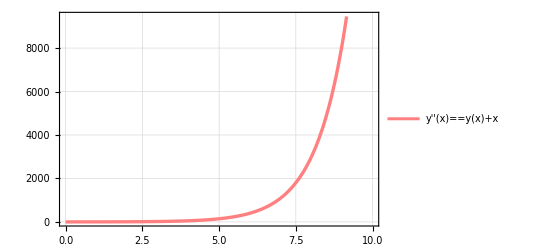

```mathematica
eq1 = y''[x]==y[x]+ x
sol4 = DSolve[{y''[x]==y[x]+ x,y[0]==0,y'[0]==1},y[x],x]
Plot[y[x]/.sol4,{x,0,10},PlotLegends->{eq1},PlotStyle->{{Pink,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

```mathematica
DSolve[{y''[x]==y[x]+ x},y[x],x]
```

{{y[x]→-x+ⅇ^x C[1]+ⅇ^-x C[2]}}

```mathematica
sol4 = DSolve[{y''[x]==y[x]+ x,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→ⅇ^-x (-1+ⅇ^(2 x)-ⅇ^x x)}}

```mathematica
sol4 = DSolve[{y''[x]==-y[x]-1,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→-1+Cos[x]+Sin[x]}}

```mathematica
DSolve[{y''[x]==(5*y'[x]-y[x])/2},y[x],x]
```

{{y[x]→ⅇ^((5/4-(√17)/4) x) C[1]+ⅇ^((5/4+(√17)/4) x) C[2]}}

```mathematica
sol4 = DSolve[{y''[x]==(5*y'[x]-y[x])/2,y[3]==6,y'[3]==-1},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {y''[x]==1/2 (-y[x]+5 y'[x]),True,True}.

DSolve[{y''[x]==1/2 (-y[x]+5 y'[x]),True,True},y[x],x]

```mathematica
DSolve[{y''[x]==1/(1+x^2)+( Sin[x])*√x},y[x],x]
```

{{y[x]→x ArcTan[x]+C[1]+x C[2]-(ⅈ ⅇ^(ⅈ x) √x (-6 √(-ⅈ x)-4 (-ⅈ x)^(3/2)+3 ⅇ^(-ⅈ x) √π Erf[√(-ⅈ x)]))/(8 √(-ⅈ x))+(ⅈ ⅇ^(-ⅈ x) √x (-6 √(ⅈ x)-4 (ⅈ x)^(3/2)+3 ⅇ^(ⅈ x) √π Erf[√(ⅈ x)]))/(8 √(ⅈ x))-(x^(3/2) Gamma[3/2,-ⅈ x])/(2 √(-ⅈ x))-(x^(3/2) Gamma[3/2,ⅈ x])/(2 √(ⅈ x))-1/2 Log[1+x^2]}}

```mathematica
sol4 = DSolve[{y''[x]==1/(1+x^2)+( Sin[x])*√x,y[0]==0,y'[0]==-2},y[x],x]
```

{{y[x]→1/(8 √(ⅈ x) √x)ⅇ^(-ⅈ x) (-6 ⅈ √(ⅈ x) x+6 ⅈ ⅇ^(2 ⅈ x) √(ⅈ x) x-2 ⅈ ⅇ^(ⅈ x) √π √(-ⅈ x) √(ⅈ x) x-16 ⅇ^(ⅈ x) √(ⅈ x) x^(3/2)+2 ⅇ^(ⅈ x) √(2 π) √(ⅈ x) x^(3/2)-2 ⅇ^(ⅈ x) √π x^2+8 ⅇ^(ⅈ x) √(ⅈ x) x^(3/2) ArcTan[x]+3 ⅇ^(ⅈ x) √π √(-ⅈ x) √(ⅈ x) Erf[√(-ⅈ x)]+3 ⅈ ⅇ^(ⅈ x) √π x Erf[√(ⅈ x)]+2 ⅇ^(ⅈ x) √π x^2 Erf[√(ⅈ x)]+2 ⅇ^(ⅈ x) √π x^2 Erfi[√(ⅈ x)]-4 ⅇ^(ⅈ x) √(ⅈ x) √x Log[1+x^2])}}

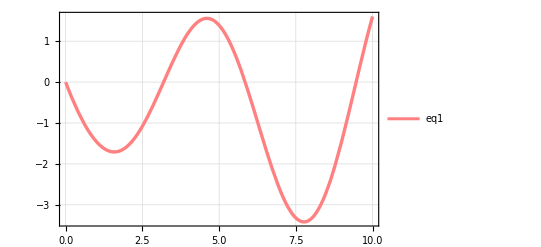

```mathematica
Plot[y[x]/.sol4,{x,0,10},PlotLegends->{eq1},PlotStyle->{{Pink,Thickness[0.006]},{Red,Thickness[0.01]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```